## Import Gillespie Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<Gillespie`
```

## Example: exponential decay

```mathematica
rxns={
makeReaction["annihilation",0.5,{"A"},{}]
};
```

```mathematica
countsInit=Association[];
countsInit["A"]=1000;
```

```mathematica
{counts,rxnCounts}=runGillespie[10.0,countsInit,rxns,{}];
```

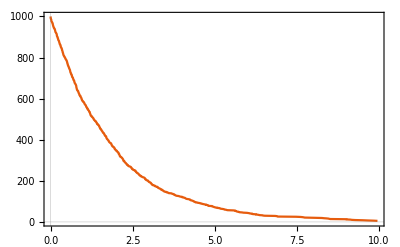

```mathematica
ListLinePlot[counts["A"]]
```

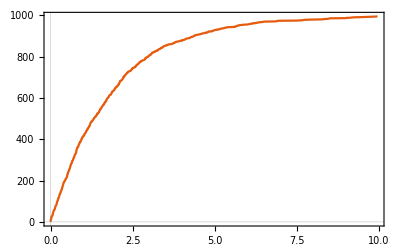

```mathematica
ListLinePlot[rxnCounts["annihilation"]]
```

## Example: exponential decay with regular writing interval

```mathematica
rxns={
makeReaction["annihilation",0.5,{"A"},{}]
};
```

```mathematica
countsInit=Association[];
countsInit["A"]=1000;
```

```mathematica
dtWrite=0.5;
```

```mathematica
{counts,rxnCounts}=runGillespie[10.0,countsInit,rxns,{},dtWrite];
```

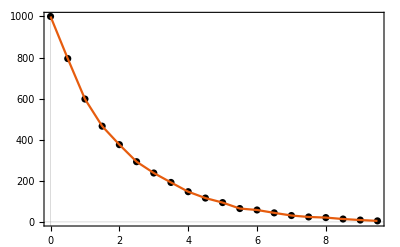

```mathematica
Show[ListPlot[counts["A"],PlotStyle->Black],ListLinePlot[counts["A"]]]
```

## Example Lotka Volterra

```mathematica
rxns={makeReaction["r1",0.01,{},{"X"}],makeReaction["r2",0.02,{"Y"},{}],makeReaction["r3",0.00001,{"X","Y"},{"Y","Y"}]};
```

```mathematica
countsInit=Association[];
countsInit["X"]=1000;
countsInit["Y"]=1000;
{counts,rxnCounts}=runGillespie[5000,countsInit,rxns,{},1.0];
```

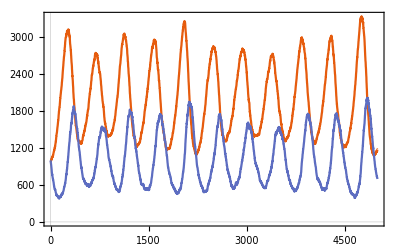

```mathematica
ListLinePlot[{counts["X"],counts["Y"]}]
```

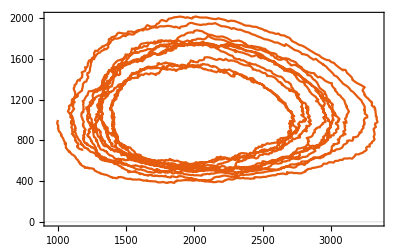

```mathematica
ListLinePlot[Transpose[{counts["X"][[;;,2]],counts["Y"][[;;,2]]}]]
```

## Example Rossler system

### Initial quantities

```mathematica
m=1;
```

```mathematica
x0q=1000*m;
y0q=8000*m;
z0q=10*m;
```

```mathematica
a1q=3000*m;
a2q=1*m;
a3q=1*m;
a4q=1650*m;
a5q=1000*m;
```

```mathematica
countsInit=Association[];
countsInit["A1"]=a1q;
countsInit["A2"]=a2q;
countsInit["A3"]=a3q;
countsInit["A4"]=a4q;
countsInit["A5"]=a5q;
countsInit["X"]=x0q;
countsInit["Y"]=y0q;
countsInit["Z"]=z0q;
```

### Reactions

```mathematica
km1=0.25;
km2=10^(-3);
km5=0.5;
kp1=1.0;
kp2=1.0;
kp3=1.0;
kp4=1.0;
kp5=1.0;
km3=1.0;
km4=1.0;
```

```mathematica
rxns={
makeReaction["rm3",km3,{"A2"},{"A5","Y"}],
makeReaction["rm4",km4,{"A3"},{"X","Z"}],
makeReaction["rp1",kp1,{"A1","X"},{"X","X"}],
makeReaction["rm1",km1,{"X","X"},{"A1","X"}],
makeReaction["rp2",kp2,{"X","Y"},{"Y","Y"}],
makeReaction["rm2",km2,{"Y","Y"},{"X","Y"}],
makeReaction["rp3",kp3,{"A5","Y"},{"A2"}],
makeReaction["rp4",kp4,{"X","Z"},{"A3"}],
makeReaction["rp5",kp5,{"A4","Z"},{"Z","Z"}],
makeReaction["rm5",km5,{"Z","Z"},{"A4","Z"}]
};
```

### Conservation laws

```mathematica
conservedSpecies={"A1","A2","A3","A4","A5"};
```

### Run

```mathematica
dtWrite=0.0001;
```

```mathematica
{counts,rxnCounts}=runGillespie[0.1,countsInit,rxns,conservedSpecies,dtWrite];
```

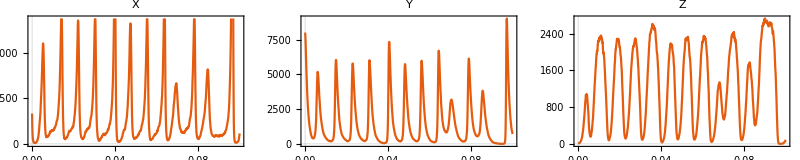

```mathematica
GraphicsRow[{
ListLinePlot[counts["X"],PlotLabel->"X"],
ListLinePlot[counts["Y"],PlotLabel->"Y"],
ListLinePlot[counts["Z"],PlotLabel->"Z"]
},ImageSize->800]
```

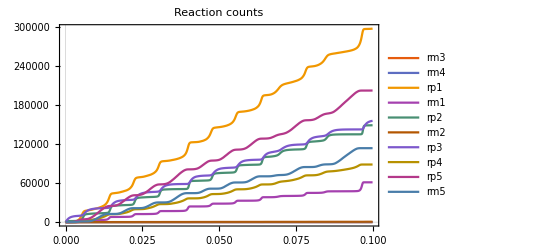

```mathematica
ListLinePlot[Values[rxnCounts],PlotLegends->Keys[rxnCounts],PlotLabel->"Reaction counts"]
```

```mathematica
plt=Show[Graphics3D@Line@Transpose[{counts["X"][[;;,2]],counts["Y"][[;;,2]],counts["Z"][[;;,2]]}],AxesLabel->{"X","Y","Z"},ImageSize->1000,AspectRatio->0.8]
```

-Graphics3D-

### PDE Soln

```mathematica
sol=NDSolve[
{
D[x[t],t]==x[t]*(a1q-km1*x[t]-z[t]-y[t])+km2*y[t]^2+a3q,
D[y[t],t]==y[t]*(x[t]-km2*y[t]-a5q)+a2q,
D[z[t],t]==z[t]*(a4q-x[t]-km5*z[t])+a3q,
x[0]==x0q,
y[0]==y0q,
z[0]==z0q
}
,{x[t],y[t],z[t]}
,{t,0,0.1}][[1]];
```

```mathematica
dat=Table[{x[t]/.sol,y[t]/.sol,z[t]/.sol},{t,0,0.1,0.0001}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

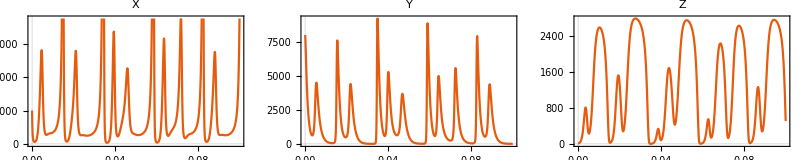

```mathematica
GraphicsRow[{
ListLinePlot[Table[{t,x[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"X"],
ListLinePlot[Table[{t,y[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"Y"],
ListLinePlot[Table[{t,z[t]/.sol},{t,0,0.1,0.0001}],PlotLabel->"Z"]
},ImageSize->800]
```

### Compare Gillespie to PDE

```mathematica
GraphicsRow[{
ListLinePlot[{counts["X"],Table[{t,x[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"X"],
ListLinePlot[{counts["Y"],Table[{t,y[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"Y"],
ListLinePlot[{counts["Z"],Table[{t,z[t]/.sol},{t,0,0.1,0.0001}]},PlotLabel->"Z",PlotLegends->{"Gillespie","PDE"}]
},ImageSize->800]
```

-Graphics-